## This is a numerical solver for the Lane Emden equation using Explicit Runge Kutta.

```mathematica
n=.
LaneEmden=1/ξ^2 D[(ξ^2 D[θ[ξ], ξ]), ξ]+θ[ξ]^n==0;

sols=NDSolve[{LaneEmden/.n->5/3,θ[0.01]==1,θ'[0.01]==0},θ,{ξ,0.01,10}, MaxSteps->100000, Method->"ExplicitRungeKutta"]
```

{{θ→InterpolatingFunction[{{0.01,10.}},<>]}}

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

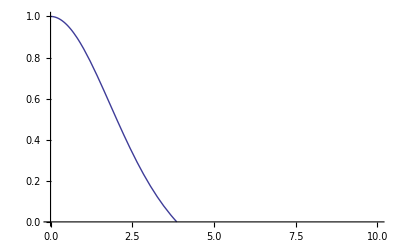

```mathematica
Plot[θ[ξ]/.sols,{ξ,0,10}]
```

```mathematica
vals=θ/.First[sols]
```

InterpolatingFunction[{{0.01,10.}},<>]

```mathematica
data=Table[{i,vals[i]},{i,0.01,4,0.01}];
```

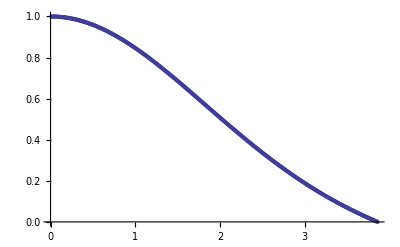

```mathematica
ListPlot[data]
```

```mathematica
(*Constants*)
μ = 1/2;
n = 3/2;
γ = (n+1)/n;
```

```mathematica
h = 6.626*10^-27 ;
me = 9.109*10^-28; 
mH = 1.673*10^-24;
κ = 1/20 * (3/Pi)^(3/2) *h^2/me * 1/(μ * mH)^(5/3);
ρc = 1.6*10^5;
G = 6.673*10^-8;
```

```mathematica
z =Select[Re[Table[data[[i]][[2]],{i,1,Length[data]}]],#>0&];
x = Table[data[[i]][[1]],{i,1,Length[z]}];
ρ = ρc z^n;
r = x *Sqrt[(n+1) κ ρ^((1-n)/n) / (4 Pi G) ];
P = κ ρ^γ;
```

```mathematica
(*Output as something useful*)
```

```mathematica
datareal = Table[{r[[i]],ρ[[i]],P[[i]]},{i,1,Length[z]}];
```

```mathematica
ListPlot[datareal]
```

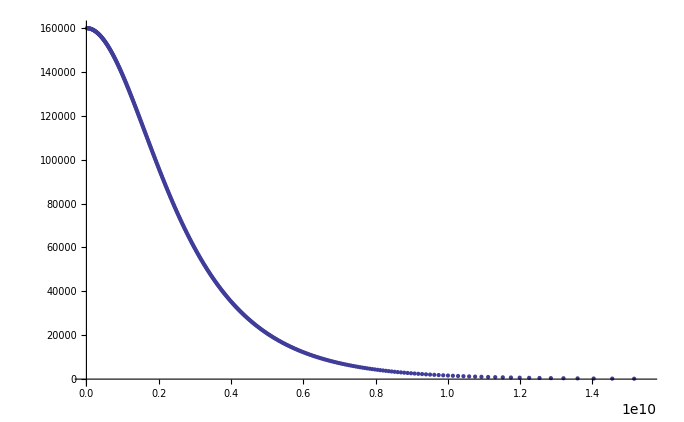

```mathematica
Export[ "/Users/kaitlin/TALENT/project1/sedov-solution/laneEmbden.dat",datareal,"Table"]
```

/Users/kaitlin/TALENT/project1/sedov-solution/laneEmbden.dat